```mathematica
Clear["Global`*"]
```

### 3. A timelike congruence in Schwarzschild.

In this exercise we study the congruence with tangent vector fields
                                                      (11)
in the standard Schwarzschild coordinate in Schwarzschild spacetime. Recall that the metric given by the line element is
.                       (12)
Symbolically the coordinate is the same as the last example. So we just need to clear a few variables.

```mathematica
Clear[u,uCov,g,ginv,h,hinv]
<<MaTeX`
```

#### 3(a). Verify the timelike and geodesic nature of the congruence

```mathematica
coord={t,r,θ,ϕ}
n=Length[coord]
```

{t,r,θ,ϕ}

4

```mathematica
(*The Schwarzschild metric*)
g=({{-(1-(2 M)/r), 0, 0, 0}, {0, (1-(2 M)/r)^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}});
ginv=FullSimplify[Inverse[g]];
MaTeX[g//MatrixForm]
MaTeX[ginv//MatrixForm]
```

-Graphics-

-Graphics-

```mathematica
(*The 4-velocity vector and 1-form*)
u=1/Sqrt[1-3 M/r]{1,0,(M/r^3)^(1/2),0};
uCov=FullSimplify[g.u];
u
uCov
```

{1/(√(1-(3 M)/r)),0,(√(M/r^3))/(√(1-(3 M)/r)),0}

{(-1+(2 M)/r)/(√(1-(3 M)/r)),0,(√(M/r^3) r^2)/(√(1-(3 M)/r)),0}

We can first verify that  is timelike.

```mathematica
FullSimplify[Transpose[u].g.u]
```

-1

Given that the 4-velocity is properly normalized, we can conclude that the parametrization is the proper time. And we should be able to verify the affine form of the geodesic equation
,                                                                 (13)
but  given the functional dependence of , and , so we just have to compute the Christoffels and verify that the second term in (13) identically vanishes.

```mathematica
affine:=FullSimplify[
Table[
(1/2)*
Sum[ginv[[i,s]]*(D[g[[s,k]],coord[[j]]]+D[g[[s,j]],coord[[k]]]-D[g[[j,k]],coord[[s]]]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}]
];
```

```mathematica
(*Display the non-zero Christoffel symbols*)
NonZeroAffineList:=Table[
If[UnsameQ[affine[[i,j,k]],0],
{Subscript[Superscript[Γ,coord[[i]]],Row[{coord[[j]],coord[[k]]}]],affine[[i,j,k]]}(*It returns a pair: the symbol and the value*)
],
{i,1,n},{j,1,n},{k,1,j}]
Partition[DeleteCases[Flatten[NonZeroAffineList],Null],2]//TableForm
```

(Γ^t)_rt | M/(r (-2 M+r))
(Γ^r)_tt | (M (-2 M+r))/r^3
(Γ^r)_rr | M/(2 M r-r^2)
(Γ^r)_θθ | 2 M-r
(Γ^r)_ϕϕ | (2 M-r) Sin[θ]^2
(Γ^θ)_θr | 1/r
(Γ^θ)_ϕϕ | -Cos[θ] Sin[θ]
(Γ^ϕ)_ϕr | 1/r
(Γ^ϕ)_ϕθ | Cot[θ]

Because , (13) for  is easily verified. The non-trivial part is for .

```mathematica
FullSimplify[Sum[affine[[1,i,j]]u[[i]]u[[j]],{i,n},{j,n}]]
```

0

It’s also verified. Although it’s obvious for the other 3 components, let’s tell the computer to verify them too.

```mathematica
Table[FullSimplify[Sum[affine[[k,i,j]]u[[i]]u[[j]],{i,n},{j,n}]]
,{k,n}]
```

{0,0,0,0}

Now it’s well verified that the congruence with tangent vector (11) is timelike, normalized and geodesic. From its component we can anticipate that it describes a motion winding around the north and south poles.

#### 3(b). Analysis of the expansion

To compute the expansion, again we first compute the covariant tensor
                                                 (14)
and the transverse metric
 .                                                   (15)

```mathematica
Clear[B]
```

```mathematica
B=Array[FullSimplify[D[uCov[[#1]],coord[[#2]]]-Sum[affine[[k,#1,#2]]uCov[[k]],
(*It's uCov that's taking the derivative!*)
{k,1,n}]]&,{n,n}];
```

```mathematica
B//MatrixForm
```

(0 | (M √(1-(3 M)/r))/(2 (-3 M+r)^2) | 0 | 0
M/(√(1-(3 M)/r) r^2) | 0 | -(√(M/r^3) r)/(√(1-(3 M)/r)) | 0
0 | -(M √(1-(3 M)/r))/(2 √(M/r^3) (-3 M+r)^2) | 0 | 0
0 | 0 | 0 | (√(M/r^3) r^2 Cos[θ] Sin[θ])/(√(1-(3 M)/r)))

Now the expansion is computed as

```mathematica
h=FullSimplify[g+Outer[Times,uCov,uCov]];
hinv=FullSimplify[ginv+Outer[Times,u,u]];
MaTeX[h//MatrixForm]
MaTeX[hinv//MatrixForm]
```

-Graphics-

-Graphics-

```mathematica
expansion=FullSimplify[Tr[hinv.B]]
Tr[hinv.B]==Tr[ginv.B]
MaTeX[expansion]
```

(√(M/r^3) Cot[θ])/(√(1-(3 M)/r))

True

-Graphics-

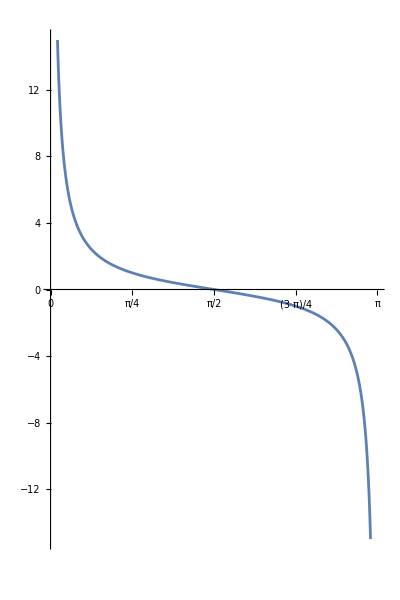

```mathematica
Plot[Cot[θ],{θ,0,π},PlotRange->{{0,π},{-15,15}},(*Set y-axis range*)Ticks->{Table[{k*Pi/4,k*Pi/4},{k,0,4}],Automatic},(*Customize x-axis ticks*)AxesLabel->{MaTeX["\\theta"],MaTeX["\\cot(\\theta)"]},(*Optional:LaTeX style labels*)PlotLabel->MaTeX["\\text{Plot of } \\cot(\\theta)"],(*Optional:LaTeX style plot label*)
BaseStyle->{FontSize->14} (*Optional:Base font size*),
AspectRatio->1.5/1]
```

This congruence comprises of the motion of a set of particles emanating from a  north pole (not the north pole of the Schwarzschild radius), and propagating “downwards” towards the mirror point  of a south pole. They are expanding in the north hemisphere while shrinking in the south hemisphere. The motion of the particles is symmetric about the equator. The points , i.e., the poles, are the cusp of the congruence. Of course the expansion is singular there.

#### 3(c). The rotation

The formula is

```mathematica
rotation=(B-Transpose[B])/2;
```

```mathematica
(*The contravariant*)
FullSimplify[ginv.rotation.Transpose[ginv]]===FullSimplify[hinv.rotation.Transpose[hinv]]
```

True

The calculation is checked to be correct.

```mathematica
rotation20=hinv.rotation.Transpose[hinv];
rotationSquared=FullSimplify[Tr[Transpose[rotation20].rotation]];
MaTeX[rotationSquared]
```

-Graphics-

#### 3(d). Check the Raychaudhuri’s equation

Recall that for timelike geodesic congruence the Raychaudhuri’s equation is 
.                                 (16)
For Schwarzschild . We have not computed the shear yet.

```mathematica
shear=(B+Transpose[B])/2-(expansion/3)*h;
MaTeX[shear//MatrixForm]
```

-Graphics-

```mathematica
FullSimplify[hinv.shear.Transpose[hinv]]===FullSimplify[ginv.shear.Transpose[ginv]]
FullSimplify[ginv.shear.Transpose[ginv]]//MatrixForm
FullSimplify[hinv.shear.Transpose[hinv]]//MatrixForm
```

True

(-(M √(M/r^3) r Cot[θ])/(3 √(1-(3 M)/r) (6 M^2-5 M r+r^2)) | -(3 M √(1-(3 M)/r) (-2 M+r))/(4 r (-3 M+r)^2) | -(M √(1-(3 M)/r) Cot[θ])/(3 r (-3 M+r)^2) | 0
-(3 M √(1-(3 M)/r) (-2 M+r))/(4 r (-3 M+r)^2) | -((1-(2 M)/r) √(M/r^3) Cot[θ])/(3 √(1-(3 M)/r)) | -(3 √(1-(3 M)/r) √(M/r^3) (-2 M+r)^2)/(4 r (-3 M+r)^2) | 0
-(M √(1-(3 M)/r) Cot[θ])/(3 r (-3 M+r)^2) | -(3 √(1-(3 M)/r) √(M/r^3) (-2 M+r)^2)/(4 r (-3 M+r)^2) | -(√(1-(3 M)/r) √(M/r^3) (-2 M+r) Cot[θ])/(3 r (-3 M+r)^2) | 0
0 | 0 | 0 | (2 √(M/r^3) Cot[θ] Csc[θ]^2)/(3 √(1-(3 M)/r) r^2))

(-(M √(M/r^3) r Cot[θ])/(3 √(1-(3 M)/r) (6 M^2-5 M r+r^2)) | -(3 M √(1-(3 M)/r) (-2 M+r))/(4 r (-3 M+r)^2) | -(M √(1-(3 M)/r) Cot[θ])/(3 r (-3 M+r)^2) | 0
-(3 M √(1-(3 M)/r) (-2 M+r))/(4 r (-3 M+r)^2) | -((1-(2 M)/r) √(M/r^3) Cot[θ])/(3 √(1-(3 M)/r)) | -(3 √(1-(3 M)/r) √(M/r^3) (-2 M+r)^2)/(4 r (-3 M+r)^2) | 0
-(M √(1-(3 M)/r) Cot[θ])/(3 r (-3 M+r)^2) | -(3 √(1-(3 M)/r) √(M/r^3) (-2 M+r)^2)/(4 r (-3 M+r)^2) | -(√(1-(3 M)/r) √(M/r^3) (-2 M+r) Cot[θ])/(3 r (-3 M+r)^2) | 0
0 | 0 | 0 | (2 √(M/r^3) Cot[θ] Csc[θ]^2)/(3 √(1-(3 M)/r) r^2))

Now we are confident about the results about the contravariant shear.

```mathematica
shear20=hinv.shear.Transpose[hinv];
(*shear20//MatrixForm*)
```

```mathematica
(*The right hand side*)
FullSimplify[-(expansion^2/3)-Tr[Transpose[shear20].shear]+rotationSquared]
```

(M Csc[θ]^2)/((3 M-r) r^2)

```mathematica
(*The left hand side*)
FullSimplify[Sum[D[expansion,coord[[i]]]u[[i]],{i,1,n}]]
```

(M Csc[θ]^2)/((3 M-r) r^2)

Something is wrong. They are not equal.

Now they are. And the result for the rotation squared is also verified. Below is just a check that the Ricci tensor indeed vanishes.

```mathematica
riemann:=riemann=FullSimplify[Table[
D[ affine[[i,l,j]],coord[[k]] ]-D[ affine[[i,k,j]],coord[[l]] ]+Sum[affine[[i,k,m]]affine[[m,l,j]]-affine[[i,l,m]]affine[[m,k,j]],{m,1,n}],
{i,1,n},{j,1,n},{k,1,n},{l,1,n}
]
];riemann04:=riemann04=FullSimplify[
Table[
Sum[g[[i,s]]riemann[[s,j,k,l]],{s,1,n}],
{i,1,n},{j,1,n},{k,1,n},{l,1,n}
]
];
ricci02:=ricci02=FullSimplify[
Table[
Sum[ginv[[k,l]]riemann04[[i,k,j,l]],{k,1,n},{l,1,n}],{i,1,n},{j,1,n}
]
];
ricci02//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)